# MGroups

## Finite Group Theory in Mathematica

Naman Taggar <namantaggar [dot] 11 [at] gmail [dot] com>

MGroups is a Mathematica Package that implements a part of Finite Group Theory. It facilitates studying group operations, order and inverses of the group elements, Cayley Tables, (ordinary and normal) subgroup structures of a group, and group morphisms easily and quickly. MGroups is licensed under the MIT Open-Source License.

## 1. Preface

In MGroups, groups are defined in the form of “Associations” that are the Mathematica version of mappings. Quite literally, a group in this package is nothing but its Cayley Table. For example, to define the Z_2 group, all that is needed is to define

How 0 operates with 0,

How 0 operates with 1,

How 1 operates with 0, and

How 1 operates with 1.

In Mathematica, Associations are of the form

```mathematica
<|a->b, c->d, e->f|>;
```

which means that a maps to b, c maps to d, and e maps to f. Now, it is only appropriate to see how Z_2 will be defined in such a way:—

```mathematica
Subscript[Z, 2]=<|0-><|0->0, 1->1|>, 1-><|0->1, 1->0|>|>;
```

... which is nothing but nested Associations. Now, if we need to see what is 0*0 in Z_2, we can type

```mathematica
Subscript[Z, 2][0][0]
```

0

to get the required output. Similarly, other complex groups are also defined.

## 2. Installation

To install the package, you can head over to my GitHub page (["github.com/zplus11/MGroups"](https://github.com/zplus11/MGroups)) and download the MGroups.m file from there. In any Mathematica Notebook, type

```mathematica
$UserBaseDirectory<>"\\Applications" (* run this to get your directory *)
```

C:\Users\Naman Taggar\AppData\Roaming\Mathematica\Applications

which should give you a folder path. Place MGroups.m file into this path on your device. Then, whenever you need to use MGroups in a Mathematica notebook, type

```mathematica
<<MGroups`
```

which will call the package. Now type

```mathematica
AdditiveGroup[2]
```

<|0→<|0→0,1→1|>,1→<|0→1,1→0|>|>

If you get the same output as above, then congratulations — you have successfully installed MGroups!

## 3. Introduction

This documentation covers each aspect of the package, from basic to advanced. We define a group first:—

Definition (Group). A group is a non-empty set in Mathematics, elements of which follow 4 properties namely Closure, Associativity, Existence of Identity, and Existence of Inverses under a certain binary operation.

### Available Groups

This package provides the groups as tabulated below.

Group | Description
AdditiveGroup | Z_n: The group {0, 1, ..., n-1} formed 
under addition modulo n.
MultiplicativeGroup | U_n: The group {0<=x<n: gcd(x,n)==1} formed
under multiplication modulo n.
DihedralGroupp | Dn: The group of symmetries of a regular 
polygon formed under their composition.
K_4 & Q_8 | Klein's 4 Group and the Quaternion Group.
ExternalDirectProduct | The External Direct Product of given groups.

They can be called by their respective function names.

### Defining a Group

Groups can be freely formed with the following command:—

```mathematica
FormGroup[{0},#[[1]]+#[[1]]&]
```

<|0→<|0→0|>|>

without having to type out the Associations yourself.

### Basic Operations

Import the package by running

```mathematica
<<MGroups`
```

Define a group using one of the functions as shown below.

```mathematica
D4=DihedralGroupp[4]; (* Caution: DihedralGroup is an inbuilt function, so this package uses DihedralGroupp *)
```

and check the domain of this group:—

```mathematica
FindDomain[D4]
```

{r0,r1,r2,r3,s0,s1,s2,s3}

Group operations can be applied just by indexing those elements through the associations.

```mathematica
D4["r2"]["s3"]
```

s1

```mathematica
D4["s1"]["s1"]
```

r0

Trying some other group:—

```mathematica
MultiplicativeGroup[13][3][4]
```

12

which is 3 × 4 (mod 13). Doing something more exciting...

```mathematica
DihedralGroupp[240]["s60"]["r190"]
```

s10

which is the composition of the 191st rotation and reflection about the 61st axis, in the Dihedral group of order 480.

External Direct Products can be formed as follows:—

```mathematica
edp1=ExternalDirectProduct[AdditiveGroup[12],MultiplicativeGroup[20], QuaternionGroup];
```

The order of this group will be 12×8×8. Let’s confirm that.

```mathematica
OrderGroup[edp1]
```

768

That is perfect! In EDPs, operations are done component-wise. For example,

```mathematica
el1={5,3,"-j"};
el2={8,19,"k"};
edp1[el1][el2]
```

{1,17,i}

### Group Properties

You can check whether a group is abelian or cyclic using AbelianQ or CyclicQ commands respectively.

```mathematica
AbelianQ[AdditiveGroup[10]]
```

True

```mathematica
AbelianQ[Klein4Group]
```

True

```mathematica
CyclicQ[DihedralGroupp[3]]
```

False

```mathematica
CyclicQ[ExternalDirectProduct[
AdditiveGroup[6],
AdditiveGroup[7]
]]
```

True

### Cayley Tables

Complete Cayley Tables can be printed for any group using CayleyTable command.

```mathematica
CayleyTable[QuaternionGroup]
```

| 1 | -1 | i | -i | j | -j | k | -k
1 | 1 | -1 | i | -i | j | -j | k | -k
-1 | -1 | 1 | -i | i | -j | j | -k | k
i | i | -i | -1 | 1 | k | -k | -j | j
-i | -i | i | 1 | -1 | -k | k | j | -j
j | j | -j | -k | k | -1 | 1 | i | -i
-j | -j | j | k | -k | 1 | -1 | -i | i
k | k | -k | j | -j | -i | i | -1 | 1
-k | -k | k | -j | j | i | -i | 1 | -1

or for an EDP:—

```mathematica
CayleyTable[ExternalDirectProduct[AdditiveGroup[2],MultiplicativeGroup[3]]]
```

| {0,1} | {0,2} | {1,1} | {1,2}
{0,1} | 0
1 | 0
2 | 1
1 | 1
2
{0,2} | 0
2 | 0
1 | 1
2 | 1
1
{1,1} | 1
1 | 1
2 | 0
1 | 0
2
{1,2} | 1
2 | 1
1 | 0
2 | 0
1

### Orders and Inverses

Table of Orders and Inverses for a group can also be printed as follows:—

```mathematica
InversesTable[DihedralGroupp[6]]
```

x | x^-1 | |x|
r0 | r0 | 1
r1 | r5 | 6
r2 | r4 | 3
r3 | r3 | 2
r4 | r2 | 3
r5 | r1 | 6
s0 | s0 | 2
s1 | s1 | 2
s2 | s2 | 2
s3 | s3 | 2
s4 | s4 | 2
s5 | s5 | 2

## 4. Subgroups

We define a subgroup.

Definition (Subgroup of a group). A subset H⊆G  is said to be a subgroup of the group G if it forms a group itself under the operation of G.

We can check this in MGroups as follows:—

```mathematica
Z20=AdditiveGroup[20]; (* {0, 1, ..., 19} *)
sub=Table[2i,{i,0,9}]; (* {0, 2, ..., 18} *)
SubgroupQ[Z20,sub]
```

True

```mathematica
SubgroupQ[DihedralGroupp[10],{"s3","r0","r2","r3"}]
```

False

The packages uses the Finite Subgroup Test to check subgroups. All subgroups can be obtained using

```mathematica
Subgroups[DihedralGroupp[5]]//TableForm
```

r0 |  |  |  |  |  |  |  |  | 
r0 | s0 |  |  |  |  |  |  |  | 
r0 | s1 |  |  |  |  |  |  |  | 
r0 | s2 |  |  |  |  |  |  |  | 
r0 | s3 |  |  |  |  |  |  |  | 
r0 | s4 |  |  |  |  |  |  |  | 
r0 | r1 | r2 | r3 | r4 |  |  |  |  | 
r0 | r1 | r2 | r3 | r4 | s0 | s1 | s2 | s3 | s4

List the cyclic subgroups of U_30:—

```mathematica
u30s=Subgroups[MultiplicativeGroup[30]];
Select[u30s,CyclicQ[<|Table[x-><|Table[y->Mod[x y,30],{y,#}]|>,{x,#}]|>]&]
```

{{1},{1,11},{1,19},{1,29},{1,7,13,19},{1,17,19,23}}

In the case of Cyclic subgroups, finding subgroups is easier (by virtue of Fundamental Theorem of Cyclic Groups). For example, even finding subgroups of U_997 (order 996) is a doable task.

```mathematica
Subgroups[MultiplicativeGroup[997]];
Length[%]
```

12

## 5. Subgroup Lattices

Most interesting, you can also see subgroup lattices of groups using this package. For example, let us see the subgroup lattice of Z_4.

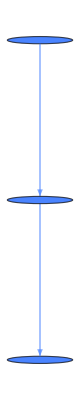

```mathematica
SubgroupLattice[AdditiveGroup[4]]
```

Here, the top most node is the group Z_4 itself, at the bottom we have {0}, and in the middle we must have {0, 2}. Let us proceed further and see something more exciting:—

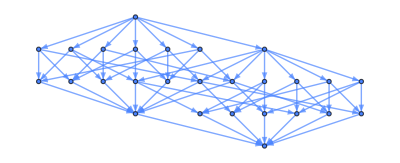

```mathematica
SubgroupLattice[MultiplicativeGroup[40]]
```

Beautiful! Subgroup Lattices of some Dihedral Groups:—

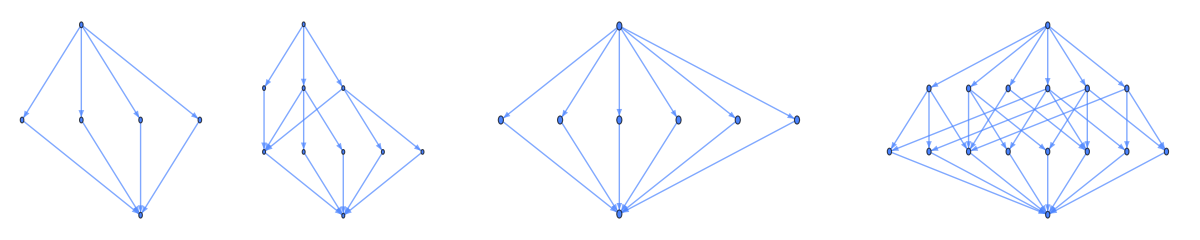

```mathematica
GraphicsRow[Table[SubgroupLattice[DihedralGroupp[i]],{i,3,6}]]
```

### Some EDPs

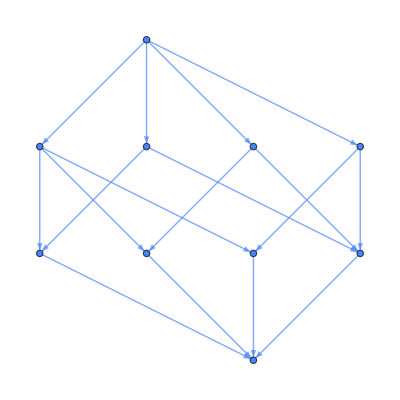

```mathematica
SubgroupLattice[ExternalDirectProduct[AdditiveGroup[6],AdditiveGroup[2]]]
```

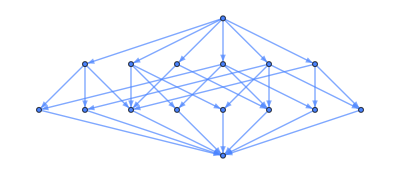

```mathematica
SubgroupLattice[ExternalDirectProduct[DihedralGroupp[3],AdditiveGroup[2]]]
```

## 6. Cosets and Normal Subgroups

Definition (Coset). If H is a subgroup of G, then for some a in G, the set {a h: h∈H} is called the left coset of H in G containing a. Subsequently, corresponding right coset is the set {h a: h∈H}.

You can define cosets in this package as follows:—

```mathematica
edp2=ExternalDirectProduct[MultiplicativeGroup[8],Klein4Group];
s={{1,"e"},{1,"c"}};(* any one subgroup *)
```

```mathematica
Coset[edp2,s,{3,"b"},"l"]
```

{{3,b},{3,a}}

```mathematica
Coset[edp2,s,{3,"b"},"r"]
```

{{3,b},{3,a}}

Both are equal.

Definition (Normal Subgroup of a group). A subgroup H of G is said to be normal in G if the left coset by every element is equal to the right counterpart.

To find normal subgroups of a group:—

```mathematica
NormalSubgroups[QuaternionGroup]//TableForm
```

1 |  |  |  |  |  |  | 
1 | -1 |  |  |  |  |  | 
1 | -1 | i | -i |  |  |  | 
1 | -1 | j | -j |  |  |  | 
1 | -1 | k | -k |  |  |  | 
1 | -1 | i | -i | j | -j | k | -k

## 7. Morphisms

Definition (Group Homomorphism). A map ϕ from G_1 to G_2 is said to be a homomorphism, if and only if it is operation preserving, i.e., if ϕ(xy)=ϕ(x)ϕ(y) ∀x,y∈G_1.

To define a Group Homomorphism, you need to define the domain, the codomain, and the map’s definition. It can be done as follows:—

```mathematica
phi=Homomorphism[
AdditiveGroup[20], (* domain *)
AdditiveGroup[2], (* co-domain *)
Mod[#,2]& (* definition in the form of a function *)
]
```

<|0→0,1→1,2→0,3→1,4→0,5→1,6→0,7→1,8→0,9→1,10→0,11→1,12→0,13→1,14→0,15→1,16→0,17→1,18→0,19→1|>

Morphisms can be visualised as follows.

```mathematica
<<MGroups`
```

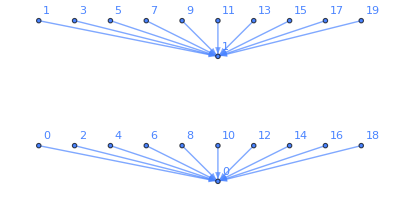

```mathematica
VisualiseMorphism[phi]
```

We can see that the kernel of phi is {0,2,...,18}.

Definition (Group Isomorphism). A homomorphism ϕ is said to be an isomorphism, if and only if it is one-one.

```mathematica
Isomorphism[
<|1-><|1->1|>|>,
<|1-><|1->1|>|>,
#&
]
```

<|1→1|>

Definition (Group Automorphism). An isomorphism from a group to itself is said to be an automorphism.

```mathematica
Automorphism[
<|1-><|1->1|>|>,
#&
]
```

<|1→1|>

Definition (Inner Automorphism). An inner automorphism is an automorphism that is induced by a group element a, with the definition x ⟶ a x a^-1.

<|r0→r0,r1→r3,r2→r2,r3→r1,s0→s2,s1→s1,s2→s0,s3→s3|>

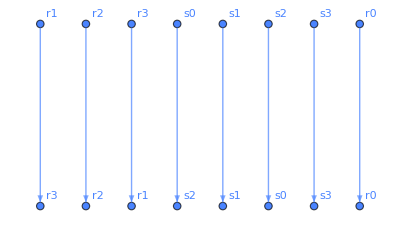

```mathematica
InnerAutomorphism[DihedralGroupp[4],"s3"]
VisualiseMorphism[%]
```

# Thank you

Github Repository: ["https://github.com/zplus11/MGroups.git"](https://github.com/zplus11/MGroups).

Copyright (c) 2024 Naman Taggar
This package is licensed under the MIT Open-Source license. See LICENSE file for more details.